```mathematica
(*Да се построи I1(f;x) за f(x)=Sqrt(x), 0≤x≤1, Xk=k/n | Xk = (k/n)^4*)
```

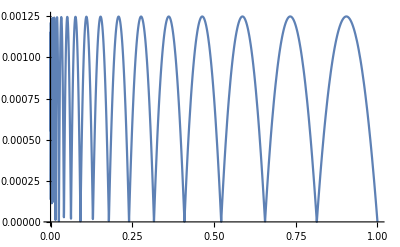

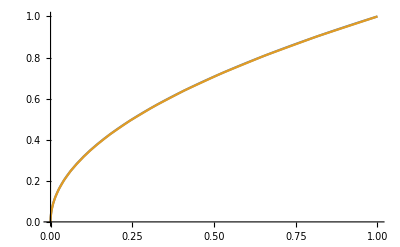

```mathematica
n = 20;
f[t_]:=Sqrt[t];
Do[x[k]=(k/n)^4, {k,0,n}];
c[0]=(f[x[0]]+f[x[n]]+(f[x[1]]-f[x[0]])/(x[1]-x[0]))/2;
c[n]=(f[x[0]]+f[x[n]]-(f[x[n]]-f[x[n-1]])/(x[n]-x[n-1]))/2;
Do[c[k]=((f[x[k+1]]-f[x[k]])/(x[k+1]-x[k])-(f[x[k]]-f[x[k-1]])/(x[k]-x[k-1]))/2,{k,1,n-1}];
I1[t_]:=Sum[c[k]*Abs[t-x[k]],{k,0,n}];
Plot[Abs[f[t]-I1[t]],{t,0,1},PlotRange->All]
Plot[{f[t],I1[t]},{t,0,1}]
```